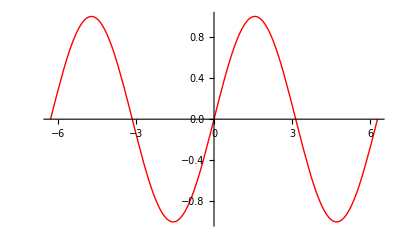

```mathematica
Clear["Global`*"]
Plot[{Sin[x]},{x,-2π,2π},Evaluate[PlotStyle-> {Directive[Red,Thick]}]]
```

```mathematica
Animate[Show[Graphics[Circle[{0,0},1]],Graphics[{Red,Disk[{Re[Exp[ⅉ t]],Im[Exp[ⅉ t]]},0.045]}], Frame -> True, PlotRange-> {{-1,1},{-1,1}},ImageSize-> Automatic],{t,0,2π},AnimationRunning-> False]
```

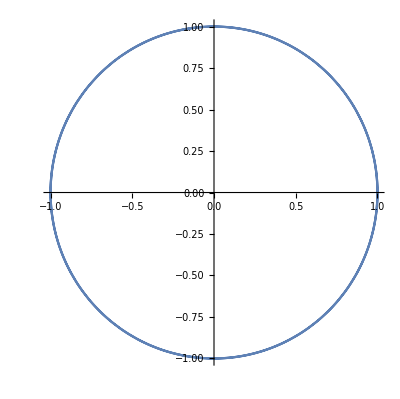

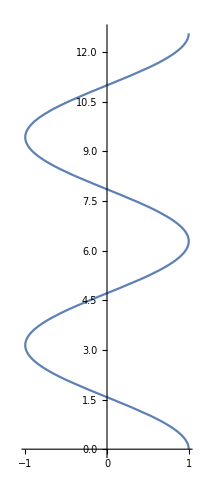

```mathematica
u[y_]:=Re[Exp[ⅉ y]];
v[y_]:=Im[Exp[ⅉ y]];
curv1=ParametricPlot[{u[y],v[y]},{y,0,4π}]
curv2=ParametricPlot[{u[y],y},{y,0,4π}]
Animate[Show[curv1,curv2,Graphics[{PointSize[Large],Red,Point[Dynamic[{u[t],v[t]}]]}],Graphics[{PointSize[Large],Blue,Point[Dynamic[{u[t],t}]]}]],{t,0,4π,AppearanceElements->None}];
```

```mathematica
u[y_]:=Re[Exp[ⅉ y]];
v[y_]:=Im[Exp[ⅉ y]];
curv1=ParametricPlot[{u[y],v[y]},{y,0,4π}];
curv2=ParametricPlot[{u[y],y},{y,0,4π}];

Animate[Show[curv1,Graphics[{Red,Disk[{Re[Exp[ⅉ t]],Im[Exp[ⅉ t]]},0.045]}],Frame -> True, PlotRange-> {{-1,1},{-1,1}},ImageSize-> Automatic],{t,0,4π},AnimationRunning-> False]Animate[Show[curv2,Graphics[{Blue,Disk[{Re[Exp[ⅉ t]],t},0.1]}], Frame -> True, PlotRange-> {{-1,1},{0,4π}},ImageSize-> Automatic],{t,0,4π},AnimationRunning-> False]
```

```mathematica
u[y_]:=Re[Exp[ⅉ y]];
v[y_]:=Im[Exp[ⅉ y]];
curv1=ParametricPlot[{u[y],v[y]},{y,0,4π}]
curv2=ParametricPlot[{u[y],-y},{y,0,4π}]
```

```mathematica
Animate[GraphicsColumn[{Show[curv1,Graphics[{Red,Disk[{Re[Exp[ⅉ t]],Im[Exp[ⅉ t]]},0.1]}],PlotRange-> {{-1,1},{-1,1}},ImageSize-> Automatic],Show[curv2,Graphics[{Red,Disk[{Re[Exp[ⅉ t]],-t},0.1]}], PlotRange-> {{-1,1},{0,-4π}},ImageSize-> 100]}],{t,0,4π},AnimationRunning-> True]
```